## Типовой расчёт Робилко Тимур, гр . 221701, Вариант 10

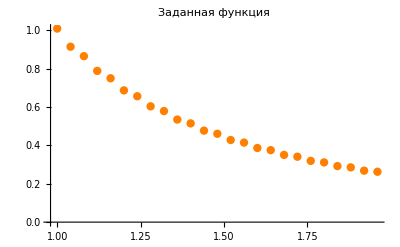

```mathematica
func = ({{1, 1.01}, {1.04, 0.915311}, {1.08, 0.865912}, {1.12, 0.789222}, {1.16, 0.750595}, {1.2, 0.6875}, {1.24, 0.656868}, {1.28, 0.604248}, {1.32, 0.57966}, {1.36, 0.535251}, {1.4, 0.515306}, {1.44, 0.477431}, {1.48, 0.461103}, {1.52, 0.428497}, {1.56, 0.415023}, {1.6, 0.386719}, {1.64, 0.375521}, {1.68, 0.350765}, {1.72, 0.341401}, {1.76, 0.319602}, {1.8, 0.311728}, {1.84, 0.292415}, {1.88, 0.285763}, {1.92, 0.268555}, {1.96, 0.262911}});
step = 0.04;
a = 1;
b = 1.96;
points = (b-a)/step+1;
funcTable = Table[{func[[i,1]],func[[i,2]]}, {i,1,points}];
pointsPlot=ListPlot[func,PlotStyle->{PointSize[0.015],Orange}, PlotLabel->"Заданная функция"];
Show[pointsPlot]
```

### Задание 1

```mathematica
Polynomial24 = InterpolatingPolynomial[funcTable, x];
plot24 = Plot[Polynomial24, {x,1,2}, PlotStyle->{Gray}];
Expand[Polynomial24]
```

3.35989×10^18-5.67593×10^19 x+4.58586×10^20 x^2-2.35829×10^21 x^3+8.66608×10^21 x^4-2.42182×10^22 x^5+5.34814×10^22 x^6-9.5727×10^22 x^7+1.41336×10^23 x^8-1.74261×10^23 x^9+1.80954×10^23 x^10-1.59145×10^23 x^11+1.18921×10^23 x^12-7.55829×10^22 x^13+4.08166×10^22 x^14-1.8669×10^22 x^15+7.19197×10^21 x^16-2.31381×10^21 x^17+6.14086×10^20 x^18-1.32112×10^20 x^19+2.24618×10^19 x^20-2.90466×10^18 x^21+2.68445×10^17 x^22-1.57934×10^16 x^23+4.4447×10^14 x^24

```mathematica
funcTable12 = Table[{func[[i,1]],func[[i,2]]},{i,1,25,2}];
Polynomial12 = InterpolatingPolynomial[funcTable12, x];
plot12 = Plot[Polynomial12, {x,1,2}, PlotStyle->{Black}];
Expand[Polynomial12]
```

374.044-3074.09 x+11774.3 x^2-27453.3 x^3+43213.9 x^4-48288. x^5+39238.8 x^6-23350.7 x^7+10096.6 x^8-3092.86 x^9+637.046 x^10-79.2108 x^11+4.49619 x^12

```mathematica
funcTable8 = Table[{func[[i,1]],func[[i,2]]},{i,1,25,3}];
Polynomial8 = InterpolatingPolynomial[funcTable8, x];
plot8 = Plot[Polynomial8, {x,1,2}, PlotStyle->{Blue}];
Expand[Polynomial8]
```

13757.1-77753.3 x+190910. x^2-265964. x^3+229959. x^4-126373. x^5+43111.6 x^6-8348.41 x^7+702.686 x^8

```mathematica
indexes = {1,6,11,16,21,25};
funcTable5 = Table[{func[[indexes[[i]],1]],func[[indexes[[i]],2]]},{i,1,6}];
Polynomial5 = InterpolatingPolynomial[funcTable5, x];
plot5 = Plot[Polynomial5, {x,1,2},PlotStyle->{Red}];
Expand[Polynomial5]
```

39.111-124.429 x+163.161 x^2-107.564 x^3+35.3468 x^4-4.61544 x^5

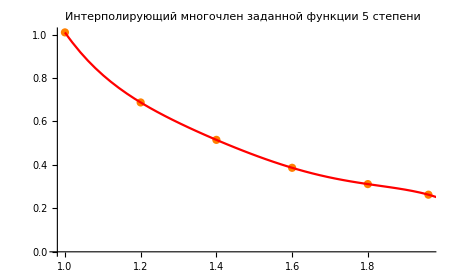

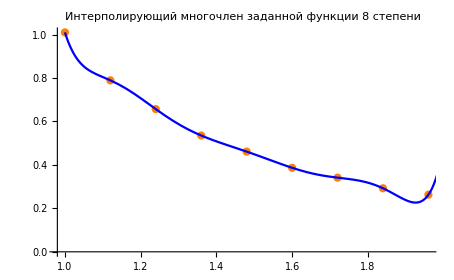

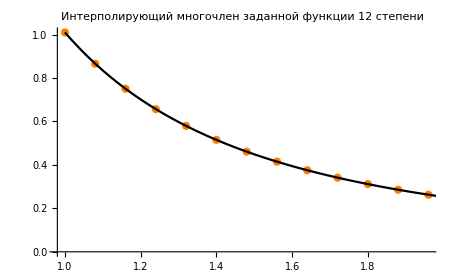

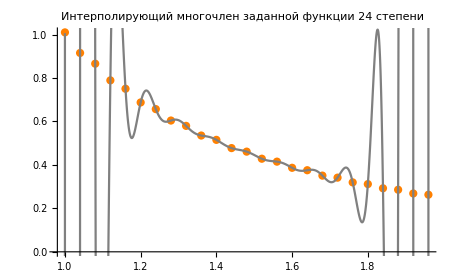

```mathematica
Show[ListPlot[funcTable5, PlotStyle->{PointSize[0.013],Orange}],plot5, PlotLabel->"Интерполирующий многочлен заданной функции 5 степени"]
Show[ListPlot[funcTable8, PlotStyle->{PointSize[0.013],Orange}],plot8,PlotLabel->"Интерполирующий многочлен заданной функции 8 степени"]
Show[ListPlot[funcTable12, PlotStyle->{PointSize[0.013],Orange}],plot12, PlotLabel->"Интерполирующий многочлен заданной функции 12 степени"]
Show[ListPlot[funcTable, PlotStyle->{PointSize[0.013],Orange}],plot24, PlotLabel->"Интерполирующий многочлен заданной функции 24 степени"]
```

```mathematica
DifferencesTable24 = Table[{funcTable[[i,1]], (Polynomial24 /. x-> funcTable[[i,1]])- funcTable[[i,2]]}, {i,1,points}];
DifferencesTable12 = Table[{funcTable[[i,1]], (Polynomial12 /. x-> funcTable[[i,1]])- funcTable[[i,2]]}, {i,1,points}];
DifferencesTable8 = Table[{funcTable[[i,1]], (Polynomial8 /. x-> funcTable[[i,1]])- funcTable[[i,2]]}, {i,1,points}];
DifferencesTable5 = Table[{funcTable[[i,1]], (Polynomial5 /. x-> funcTable[[i,1]])- funcTable[[i,2]]}, {i,1,points}];
```

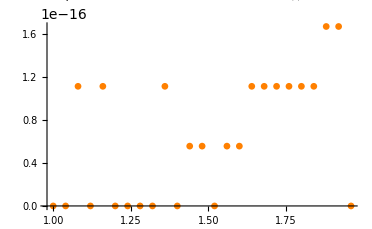

1.78726×10^-31

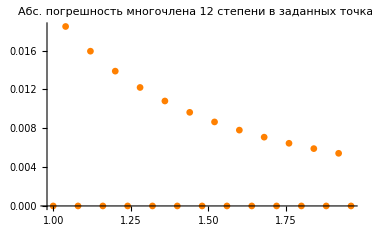

0.00144011

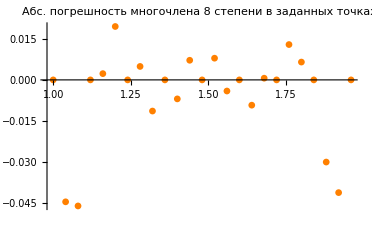

0.00771268

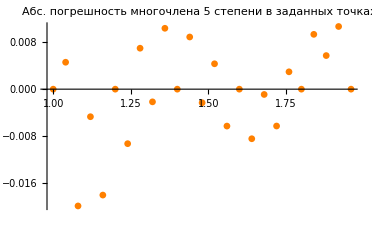

0.00151517

```mathematica
Show[ListPlot[DifferencesTable24, PlotStyle->{PointSize[0.013],Orange}], PlotLabel->"Абс. погрешность многочлена 24 степени в заданных точках"]
Polynomial24S = Sum[((Polynomial24/.x->func[[i,1]])-func[[i,2]])^2, {i,points}]
Show[ListPlot[DifferencesTable12, PlotStyle->{PointSize[0.013],Orange}], PlotLabel->"Абс. погрешность многочлена 12 степени в заданных точках"]
Polynomial12S = Sum[((Polynomial12/.x->func[[i,1]])-func[[i,2]])^2, {i,points}]
Show[ListPlot[DifferencesTable8, PlotStyle->{PointSize[0.013],Orange}], PlotLabel->"Абс. погрешность многочлена 8 степени в заданных точках"]
Polynomial8S = Sum[((Polynomial8/.x->func[[i,1]])-func[[i,2]])^2, {i,points}]
Show[ListPlot[DifferencesTable5, PlotStyle->{PointSize[0.013],Orange}], PlotLabel->"Абс. погрешность многочлена 5 степени в заданных точках"]
Polynomial5S = Sum[((Polynomial5/.x->func[[i,1]])-func[[i,2]])^2, {i,points}]
```

Таким образом, наилучшим в сравнении по сумме квадратов разностей функции в заданных узлах оказался многочлен 24-й степени. По графикам можно заметить, что погрешность увеличивается ближе к крайним значениям интерполируемой функции .  Несмотря на это, интерполяция не гарантирует, что поведение полученной функции между узлами интерполяции будет повторять поведение исходной функции. Об этом свидетельствует увеличение погрешности в узлах, которые не были выбраны для интерполяции 12, 8 и 5 степеней, а также графики многочленов высоких степеней (в частности, ближе к крайним значениям отрезка интерполяции).

### Задание 2

```mathematica
Spline5:=Interpolation[funcTable5,x,Method->"Spline"]
SplinePlot5 = Plot[Spline5, {x,1,2}, PlotStyle->{Red}];
Spline8:=Interpolation[funcTable8,x,Method->"Spline"]
SplinePlot8 = Plot[Spline8, {x,1,2}, PlotStyle->{Blue}];
Spline12:=Interpolation[funcTable12,x,Method->"Spline"]
SplinePlot12 = Plot[Spline12, {x,1,2}, PlotStyle->{Black}];
Spline24:=Interpolation[funcTable,x,Method->"Spline"]
SplinePlot24 = Plot[Spline24, {x,1,2}, PlotStyle->{Gray}];
```

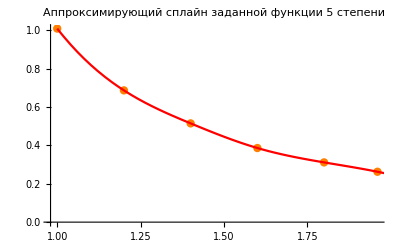

0.00113297

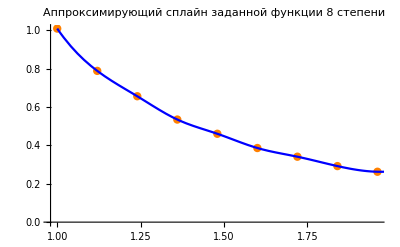

0.0010783

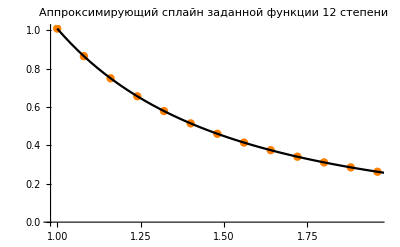

0.00144203

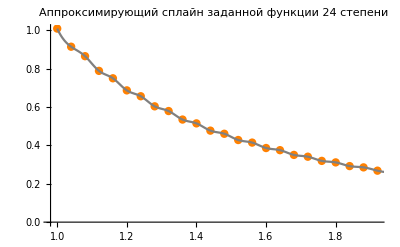

1.17097×10^-31

```mathematica
Show[ListPlot[funcTable5, PlotStyle->{PointSize[0.015],Orange}],SplinePlot5, PlotLabel->"Аппроксимирующий сплайн заданной функции 5 степени"]
Spline5S =Sum[((Spline5/.x->func[[i,1]])-func[[i,2]])^2, {i,points}]
Show[ListPlot[funcTable8, PlotStyle->{PointSize[0.015],Orange}],SplinePlot8,PlotLabel->"Аппроксимирующий сплайн заданной функции 8 степени"]
Spline8S =Sum[((Spline8/.x->func[[i,1]])-func[[i,2]])^2, {i,points}]
Show[ListPlot[funcTable12, PlotStyle->{PointSize[0.015],Orange}],SplinePlot12, PlotLabel->"Аппроксимирующий сплайн заданной функции 12 степени"]
Spline12S =Sum[((Spline12/.x->func[[i,1]])-func[[i,2]])^2, {i,points}]
Show[ListPlot[funcTable24, PlotStyle->{PointSize[0.015],Orange}],SplinePlot24, PlotLabel->"Аппроксимирующий сплайн заданной функции 24 степени"]
Spline24S =Sum[((Spline24/.x->func[[i,1]])-func[[i,2]])^2, {i,points}]
```

Таким образом, наилучшим в сравнении по сумме квадратов разностей функции в заданных узлах оказался сплайн 24 - й степени . Погрешность оказалась меньше, чем в случае интерполяционного многочлена из задания 1.

### Задание 3

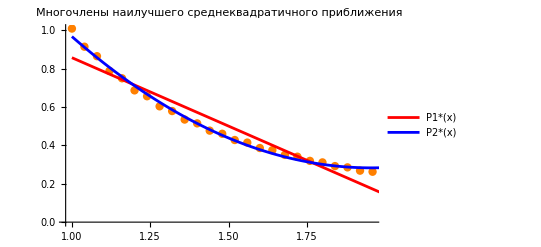

```mathematica
P1=Fit[funcTable,{1,x},x];
P2=Fit[funcTable,{1,x, x^2},x];
PPlot = Plot[{P1,P2}, {x,1,2},PlotStyle->{Red, Blue}, PlotLegends->{"P1*(x)","P2*(x)"}];
Show[ListPlot[funcTable, PlotStyle->{PointSize[0.015],Orange}],PPlot, PlotLabel->"Многочлены наилучшего
cреднеквадратичного приближения"]
```

```mathematica
S1 = Sum[((P1/.x->func[[i,1]])-func[[i,2]])^2, {i,points}]
S2 = Sum[((P2/.x->func[[i,1]])-func[[i,2]])^2, {i,points}]
```

0.0828803

0.00547391

Таким образом, многочлен наилучшего cреднеквадратичного приближения второго порядка показал лучшую точность как графически, так и исходя из высчитанной суммы квадратов разностей

### Задание 4

#### Метод левых прямоугольников

```mathematica
(*For[i=1,i<=points,i++, Subscript[x, i]=step+Subscript[x, i-1];]*)
LeftRectangle=step*∑_(i=1)^(points-1) func[[i,2]]
```

0.504976

#### Метод правых прямоугольников

```mathematica
RightRectangle=step*∑_(i=2)^points func[[i,2]]
```

0.475092

#### Метод средних прямоугольников

```mathematica
AverageRectangle=step*∑_(i=1)^(points-1) (func[[i,2]]+func[[i+1,2]])/2 (* В данном случае аналогичен методу трапеций, так как функция задана таблично и значение функции в середине отрезка принимается среднему арифметическому крайних значений на отрезке *)
```

0.490034

#### Метод трапеций

```mathematica
Trapezoidal=step*∑_(i=1)^(points-1) (func[[i,2]]+func[[i+1,2]])/2
```

0.490034

#### Метод Симпсона

```mathematica
n = 12;
h = (b-a)/(2n);
For[i=0,i<=2*n,i++, Subscript[y, i]=func[[i+1,2]];]
Simpsons=∑_(i=0)^(n-1) h/3*(Subscript[y, 2i]+4 Subscript[y, 2i+1]+Subscript[y, 2i+2])
```

0.48817

Таким образом, методы правых и левых прямоугольников могут давать завышенные или заниженные результаты в зависимости от производной исходной функции . Методы трапеций и Симпсона позволяют получить более точный результат .

### Задание 5

#### Первая производная (1 порядок точности)

```mathematica
FirstDerivativesFirstAccuracy=Table[{i,func[[i,1]],(func[[i+1,2]]-func[[i,2]])/step},{i,1,points-1}]; (* Узлы 1-24 *)
TableForm[FirstDerivativesFirstAccuracy,TableHeadings->{None,{"Узел","x_i","y'_i"}}, ]
```

Узел | x_i | y'_i
1 | 1 | -2.36723
2 | 1.04 | -1.23497
3 | 1.08 | -1.91725
4 | 1.12 | -0.965675
5 | 1.16 | -1.57738
6 | 1.2 | -0.7658
7 | 1.24 | -1.3155
8 | 1.28 | -0.6147
9 | 1.32 | -1.11022
10 | 1.36 | -0.498625
11 | 1.4 | -0.946875
12 | 1.44 | -0.4082
13 | 1.48 | -0.81515
14 | 1.52 | -0.33685
15 | 1.56 | -0.7076
16 | 1.6 | -0.27995
17 | 1.64 | -0.6189
18 | 1.68 | -0.2341
19 | 1.72 | -0.544975
20 | 1.76 | -0.19685
21 | 1.8 | -0.482825
22 | 1.84 | -0.1663
23 | 1.88 | -0.4302
24 | 1.92 | -0.1411

#### Первая производная (2 порядок точности)

```mathematica
FirstDerivativesSecondAccuracy=Table[{i,func[[i,1]],(func[[i+1,2]]-func[[i-1,2]])/(2*step)},{i,2,points-1}]; (* Узлы 2-24 *)
TableForm[FirstDerivativesSecondAccuracy,TableHeadings->{None,{"Узел","x_i","y'_i"}}, ]
```

Узел | x_i | y'_i
2 | 1.04 | -1.8011
3 | 1.08 | -1.57611
4 | 1.12 | -1.44146
5 | 1.16 | -1.27152
6 | 1.2 | -1.17159
7 | 1.24 | -1.04065
8 | 1.28 | -0.9651
9 | 1.32 | -0.862462
10 | 1.36 | -0.804425
11 | 1.4 | -0.72275
12 | 1.44 | -0.677538
13 | 1.48 | -0.611675
14 | 1.52 | -0.576
15 | 1.56 | -0.522225
16 | 1.6 | -0.493775
17 | 1.64 | -0.449425
18 | 1.68 | -0.4265
19 | 1.72 | -0.389538
20 | 1.76 | -0.370913
21 | 1.8 | -0.339838
22 | 1.84 | -0.324563
23 | 1.88 | -0.29825
24 | 1.92 | -0.28565

#### Вторая производная (2 порядок точности)

```mathematica
SecondDerivativesSecondAccuracy=Table[{i,func[[i,1]],(func[[i+1,2]]-2*func[[i,2]]+func[[i-1,2]])/step^2},{i,2,points-1}]; 
TableForm[SecondDerivativesSecondAccuracy,TableHeadings->{None,{"Узел","x_i","y('')_i"}}, ]
```

Узел | x_i | y('')_i
2 | 1.04 | 28.3063
3 | 1.08 | -17.0569
4 | 1.12 | 23.7894
5 | 1.16 | -15.2925
6 | 1.2 | 20.2894
7 | 1.24 | -13.7425
8 | 1.28 | 17.52
9 | 1.32 | -12.3881
10 | 1.36 | 15.29
11 | 1.4 | -11.2063
12 | 1.44 | 13.4669
13 | 1.48 | -10.1737
14 | 1.52 | 11.9575
15 | 1.56 | -9.26875
16 | 1.6 | 10.6913
17 | 1.64 | -8.47375
18 | 1.68 | 9.62
19 | 1.72 | -7.77188
20 | 1.76 | 8.70313
21 | 1.8 | -7.14938
22 | 1.84 | 7.91313
23 | 1.88 | -6.5975
24 | 1.92 | 7.2275

Таким образом, использование формул численного дифференцирования может дать удовлетворительные результаты для нахождения производных 1 и 2 порядка . Однако при шаге сетки, близком к нулю, неустранимые погрешности в значениях функции оказывают сильное влияние на результат (замечание из лекции 10), о чём свидетельствуют вычисленные значения 2 - й производной .